# Kelvin problem (2-d plane strain)

## Integrate point source over 2-d surfaces

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx);
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy);
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy);
```

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxIndef = Integrate[ReplaceAll[ux,ys->0],xs,GeneratedParameters->C];
uxDef = ReplaceAll[uxIndef,{xs->w}]-ReplaceAll[uxIndef,{xs->-w}]//FullSimplify
uyIndef = Integrate[ReplaceAll[uy,ys->0],xs,GeneratedParameters->C];
uyDef = ReplaceAll[uyIndef,{xs->w}]-ReplaceAll[uyIndef,{xs->-w}]//FullSimplify
```

1/(16 π μ (-1+ν))(16 fx w (-1+ν)-8 fx yo (-1+ν) ArcTan[(w-xo)/yo]-8 fx yo (-1+ν) ArcTan[(w+xo)/yo]+(fy yo-fx (w-xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]-(fy yo+fx (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2])

1/(16 π μ (-1+ν))(4 fy w (-3+4 ν)+4 fy yo (-1+2 ν) ArcTan[(-w+xo)/yo]+4 fy yo (1-2 ν) ArcTan[(w+xo)/yo]+(fx yo+fy (-w+xo) (-3+4 ν)) Log[(w-xo)^2+yo^2]-(fx yo+fy (w+xo) (-3+4 ν)) Log[(w+xo)^2+yo^2])

## Surface Integral over some arbitrary shape

```mathematica
vertices={{-1,0},{1,0},{0,1}};
(*Step 2:Define the function to integrate*)
f=sxy;
(*Step 3:Define the region of integration*)
region=Triangle[vertices];
(*region = Rectangle[{0,0},{w,w}];*)
(*Step 4:Perform the integration*)
(*uxTri=SurfaceIntegrate[f,{xs,ys}∈region]//FullSimplify*)
uxTri=Integrate[f,{xs,ys}∈region]
```

-1/(8 (π-π ν))(-2 fx+(-fy (1+xo-yo) (-1+2 ν)+fx (-1-3 yo+2 ν+2 yo ν+xo (-1+2 ν))) ArcTan[(-1+xo)/yo]-(-fy (1+xo-yo) (-1+2 ν)+fx (-1-3 yo+2 ν+2 yo ν+xo (-1+2 ν))) ArcTan[(1+xo)/yo]-2 (fx xo+fy (-1+yo)) (-1+2 ν) ArcTan[(-1-xo+yo)/(-1+xo+yo)]+2 (fx xo+fy (-1+yo)) (-1+2 ν) ArcTan[(1-xo+yo)/(-1+xo+yo)]+2 (fx-fy) (-1+2 ν) ArcTan[(-1+xo+yo)/(-1+xo-yo)]+2 (fx-fy) (-1+2 ν) ArcTan[(-1+xo+yo)/(1-xo+yo)]+2 (fx+fy xo-fx yo) (-1+ν) Log[xo^2+(-1+yo)^2]-2 (fx+fy xo-fx yo) (-1+ν) Log[1-2 xo+xo^2+yo^2]+(fx (1+xo-yo) (-1+ν)+fy (-1+xo (-1+ν)+ν+yo ν)) Log[1-2 xo+xo^2+yo^2]-(fx (1+xo-yo) (-1+ν)+fy (-1+xo (-1+ν)+ν+yo ν)) Log[1+2 xo+xo^2+yo^2])

```mathematica
Collect[uxTri,{fx,fy,μ(-1+ν)},FullSimplify]
```

-1/(32 π μ (-1+ν))fy (2+(1+xo-yo)^2 ArcTan[yo/(-1+xo)]-(1+xo-yo)^2 ArcTan[yo/(1+xo)]+2 (-1+xo+yo+(xo^2+(-1+yo)^2) ArcTan[(-1+xo+yo)/(1+xo-yo)]+((-1+xo)^2+yo^2) ArcTan[(-1+xo+yo)/(1-xo+yo)])+4 (-xo+yo) ArcTan[1+(2 yo)/(-1+xo-yo)]-yo (2+yo Log[(-1+xo)^2+yo^2])+yo^2 Log[(1+xo)^2+yo^2])-1/(32 π μ (-1+ν))fx (22-4 (2+xo)-16 ν+4 yo ArcTan[(-1+xo)/yo]-4 (1+xo) yo ArcTan[(-1+xo)/yo]-4 yo ArcTan[(1+xo)/yo]+4 (1+xo) yo ArcTan[(1+xo)/yo]+2 (3-4 ν) (-1+xo+yo+(xo^2+(-1+yo)^2) ArcTan[(-1+xo+yo)/(1+xo-yo)]+((-1+xo)^2+yo^2) ArcTan[(-1+xo+yo)/(1-xo+yo)])+2 (-1+xo) Log[(-1+xo)^2+yo^2]+(3-xo (2+xo)+yo^2) Log[(-1+xo)^2+yo^2]+2 (-2-xo+yo+(1+xo-yo) (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+(1+xo-yo) (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]-xo (-1+yo) Log[xo^2+(-1+yo)^2]+(1+xo (-1+yo)) Log[(-1+xo)^2+yo^2])-4 (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])+2 xo (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])+4 yo (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])+4 ν (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])-4 xo ν (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])-4 yo ν (-4+2 (-1+xo+yo) ArcTan[(1+xo-yo)/(-1+xo+yo)]+2 (-1+xo+yo) ArcTan[(1-xo+yo)/(-1+xo+yo)]+(1+xo-yo) Log[xo^2+(-1+yo)^2]+(1-xo+yo) Log[(-1+xo)^2+yo^2])-2 (1+xo) Log[(1+xo)^2+yo^2]+(1+xo-yo) (1+xo+yo) Log[(1+xo)^2+yo^2]+2 xo (4+2 yo ArcTan[(-1+xo)/yo]-2 yo ArcTan[(1+xo)/yo]+(-1+xo) Log[(-1+xo)^2+yo^2]-(1+xo) Log[(1+xo)^2+yo^2])+4 ν (-4+2 yo (ArcTan[(1-xo)/yo]+ArcTan[(1+xo)/yo])-(-1+xo) Log[(-1+xo)^2+yo^2]+(1+xo) Log[(1+xo)^2+yo^2])+4 xo ν (-4+2 yo (ArcTan[(1-xo)/yo]+ArcTan[(1+xo)/yo])-(-1+xo) Log[(-1+xo)^2+yo^2]+(1+xo) Log[(1+xo)^2+yo^2])+(3-4 ν) ((1+xo-yo)^2 ArcTan[yo/(-1+xo)]-(1+xo-yo)^2 ArcTan[yo/(1+xo)]+4 (-xo+yo) ArcTan[1+(2 yo)/(-1+xo-yo)]-yo (2+yo Log[(-1+xo)^2+yo^2])+yo^2 Log[(1+xo)^2+yo^2])-2 ν (-4 (2+xo)-4 (1+xo) yo ArcTan[(-1+xo)/yo]+4 (1+xo) yo ArcTan[(1+xo)/yo]+(3-xo (2+xo)+yo^2) Log[(-1+xo)^2+yo^2]+(1+xo-yo) (1+xo+yo) Log[(1+xo)^2+yo^2])-8 yo (yo (ArcTan[(1-xo)/yo]+ArcTan[(1+xo)/yo])+1/2 (-4-(-1+xo) Log[(-1+xo)^2+yo^2]+(1+xo) Log[(1+xo)^2+yo^2]))+8 yo ν (yo (ArcTan[(1-xo)/yo]+ArcTan[(1+xo)/yo])+1/2 (-4-(-1+xo) Log[(-1+xo)^2+yo^2]+(1+xo) Log[(1+xo)^2+yo^2])))

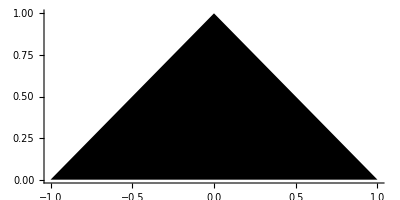

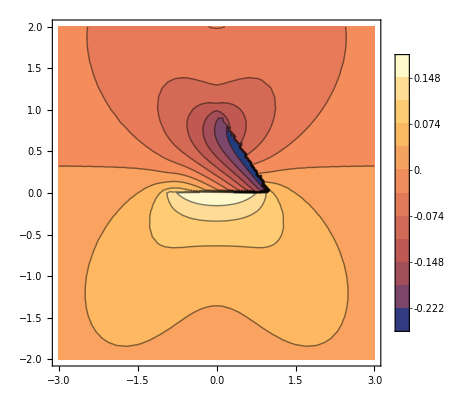

```mathematica
Graphics[{ReplaceAll[region,{w->1,L->2}]},Axes->True]
ContourPlot[ReplaceAll[uxTri,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```